```mathematica
(* Model parameters *)
ρ=1.0;
β=0.0;
α=0.08;
n=3.0;
Nsteps=100;

(* Adaptive RK parameters *)
Tmax=120;
h0 = 0.01;
tol = 0.1;
```

```mathematica
generateRandomInitialSurface[Nsteps_Integer]:=Module[{list,var},list=Range[1,Nsteps]*1.0;
var=0.2;
For[i=1,i<=Nsteps,i++,
list[[i]]=i-1+(1.0-var)+RandomReal[]*2.0*var
];
Return[list]
]
```

```mathematica
y0 = generateRandomInitialSurface[Nsteps];
```

```mathematica
velocityMM1[t_, Y_List]:=Module[{M,DY,d,d3,i,dtemp,dtem},

M=Length[Y];
d=ConstantArray[0.,M+1];
d3=ConstantArray[0.,M+1];

(* Calculate step-step distances *)
For[i=2,i<=M,i++,
dtemp=Y[[i]]-Y[[i-1]];
d[[i]]=dtemp^ρ;
d3[[i]]=1./(dtemp^n)
];

(* Apply periodic B.C.*)
dtem=Y[[1]]-Y[[M]]+M;
d[[1]]=dtem^ρ;
d[[M+1]]=d[[1]];

d3[[1]]=1./(dtem^n);
d3[[M+1]]=d3[[1]];

(* Calculate step velocities*)
DY=Table[d[[i]]+β*d[[i+1]]-α*(d3[[i+1]]-d3[[i]]),{i,1,M}];

Return [DY];
]
```

```mathematica
RK23[f_,u0_,t0_,T_, h0_, tol_]:= Module[{i,t,y,h,hs, k1,k2,k3},

t={t0};
y = {u0};
h = h0;
hs = {h};
i= 1;
Monitor[While[t⟦i⟧ ≤ T,
k1 = h*f[t⟦i⟧, y⟦i⟧];
k2 = h*f[t⟦i⟧+h, y⟦i⟧+k1];
k3 = h*f[t⟦i⟧+h/2, y⟦i⟧+k1/4 + k2/4];

While[Norm[1/3 (-k1-k2+2 k3),Infinity]/1> tol,
h= h*(tol/Norm[1/3 (-k1-k2+2 k3),Infinity])^(1/3);
k1 = h*f[t⟦i⟧, y⟦i⟧];
k2 = h*f[t⟦i⟧+h, y⟦i⟧+k1];
k3 = h*f[t⟦i⟧+h/2, y⟦i⟧+k1/4 + k2/4];
]; 
y  = Append[y, y⟦i⟧+k1/6+k2/6+(2*k3)/3];
t = Append[t, t⟦i⟧+h];
hs = Append[hs,h];
i+=1;
h= h*(tol/Norm[1/3 (-k1-k2+2 k3),Infinity])^(1/3);
];, ProgressIndicator[t[[i]]/T]];
Return[{t,y,hs}];
];
PC4[f_,u0_,t0_, T_, h_]:= Module[{y,fi,i,k1,k2,k3,k4, t,n,ypred,j, correctorSteps=4},
n = Ceiling[(T-t0)/h];
t = Table[0+i*h,{i,0,n}];
y = Table[u0, {i,0,n}];
fi= Table[f[t0, u0], {i,0,n}];

(* Start with explicit runge kutta 4 to generate initial points *)
For[i = 1, i≤ 3,i++,
k1 = h*f[t⟦i⟧,y⟦i⟧];
k2 = h*f[t⟦i⟧+h/2,y⟦i⟧+k1/2];
k3 = h*f[t⟦i⟧+h/2,y⟦i⟧+k2/2];
k4 = h*f[t⟦i⟧+h,y⟦i⟧+k3];
y⟦i+1⟧ = y⟦i⟧ + k1/6 + k2/3 + k3/3 +k4/6;
fi[[i+1]]=f[t⟦i⟧+h,y[[i+1]]];
];


Monitor[For[i=4, i<= n,i++,
(* Predictor Adams-Bashforth 4*)
ypred= y[[i]]+h/24(55*fi[[i]]-59fi[[i-1]]+37*fi[[i-2]]-9fi[[i-3]]);
(* Corrector Adams-Moulton 4*)
For[j = 1, j<= correctorSteps, j++,
ypred= y[[i]] +h/720(251f[t[[i]]+h, ypred]+646fi[[i]]-264fi[[i-1]]+106fi[[i-2]]-19fi[[i-3]]);
];

(* Save result *)
y[[i+1]]= y[[i]] +h/720(251f[t[[i]]+h, ypred]+646fi[[i]]-264fi[[i-1]]+106fi[[i-2]]-19fi[[i-3]]);
fi[[i+1]] = f[t[[i]]+h, y[[i+1]] ];
];, ProgressIndicator[i/n]];

Return[{t,y}];
];
```

```mathematica
(*{tsol,ysol}=PC4[velocityMM1, y0, 0,Tmax, 0.1];
ListLinePlot[Table[Transpose[{tsol,ysol[[All, i]]}],{i,1,Nsteps,2}]]*)
```

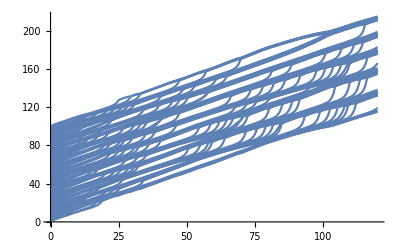

```mathematica
sol=NDSolve[{x'[t]==velocityMM1[t, x[t]], x[0]==y0},x,{t,0,Tmax}, Method->{"TimeIntegration"->"StiffnessSwitching"} ][[1]];
trajetories=(x/.sol);
Plot[(trajetories[t]),{t,0,Tmax}]
```